## Tustin pre-warping (Problem 5.12)

```mathematica
Clear["Global`*"];
```

```mathematica
G0 = TransferFunctionModel[1/(s^2+2 ζ s + 1),s]
```

1/(1+2 ζ s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
G0d= ToDiscreteTimeModel[G0,Ts/.Ts->2,z,Method -> "BilinearTransform"]
```

(1+z)^2/(2 (1-ζ+z^2+ζ z^2))2TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11481FalseFalseFalseAutomaticNoneAutomatic

```mathematica
G1d= ToDiscreteTimeModel[G0,Ts/.Ts->2,z,Method -> {"BilinearTransform","CriticalFrequency"->ω}]//Simplify
```

((1+z)^2 Tan[ω]^2)/(ω^2 (-1+z)^2+2 ζ ω (-1+z^2) Tan[ω]+(1+z)^2 Tan[ω]^2)2TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z111-11FalseFalseFalseAutomaticNoneAutomatic

```mathematica
G1d/.ζ->0.1//N
```

((1.+z)^2 Tan[ω]^2)/(ω^2 (-1.+z)^2+0.2 ω (-1.+z^2) Tan[ω]+(1.+z)^2 Tan[ω]^2)2.TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z111.-1.1FalseFalseFalseAutomaticNoneAutomatic

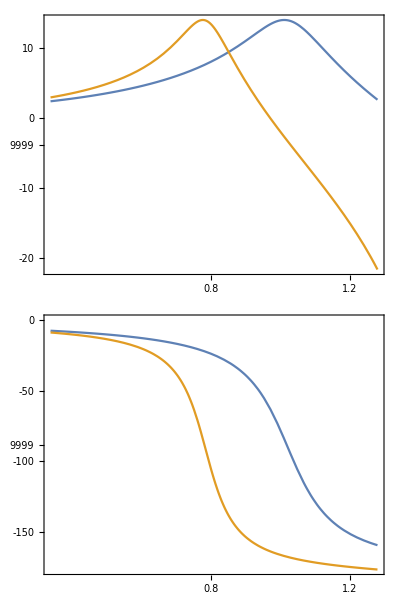

```mathematica
BodePlot[{G0/.ζ->0.1,G0d/.ζ->0.1,G1d/.ζ->0.1},{0.5,1.3}]
```

Note:  the frequency scale is "warped" ω → 2/T Tan[ω T/2]

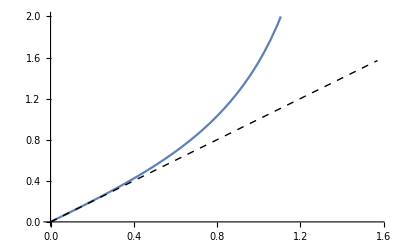

```mathematica
ω1 = 2/Ts Tan[ω Ts/2];
Plot[{ 2/Ts Tan[ω Ts/2]/.Ts->2,ω},{ω,0,π/2},PlotRange->{0,2},PlotStyle->{,{Black,Dashed,Thin}}]
```

```mathematica
Series [Tan[ω ],{ω,0,5}]
```

ω+ω^3/3+(2 ω^5)/15+O[ω]^6

```mathematica
{1/Tan[1],(1/Tan[1])^2}//N
```

{0.642093,0.412283}